```mathematica
MyList[n_,p_]:=ReadList[StringJoin["d:\\Triangle\\Data\\",ToString[n],"_",ToString[p],".txt"],Number]
```

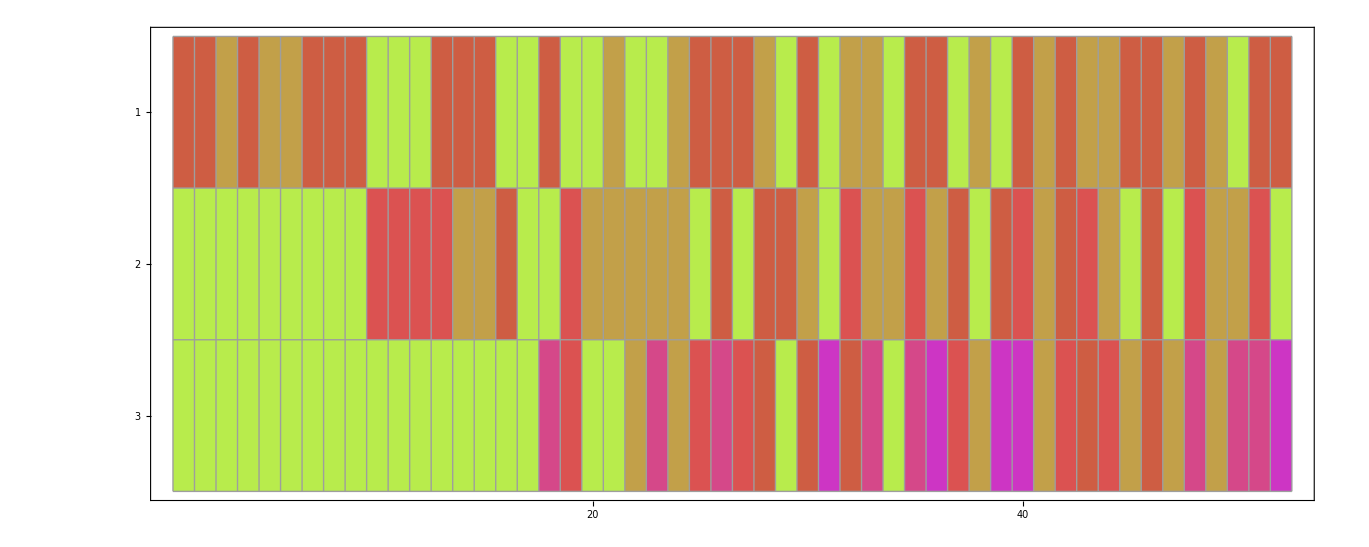

```mathematica
ArrayPlot[Table[ IntegerDigits[1091606241026315893893358160959567012,b,52],{b,{5,7,11}}],Frame->True,FrameTicks->Automatic,Mesh->True,ColorFunction->"NeonColors"]
```

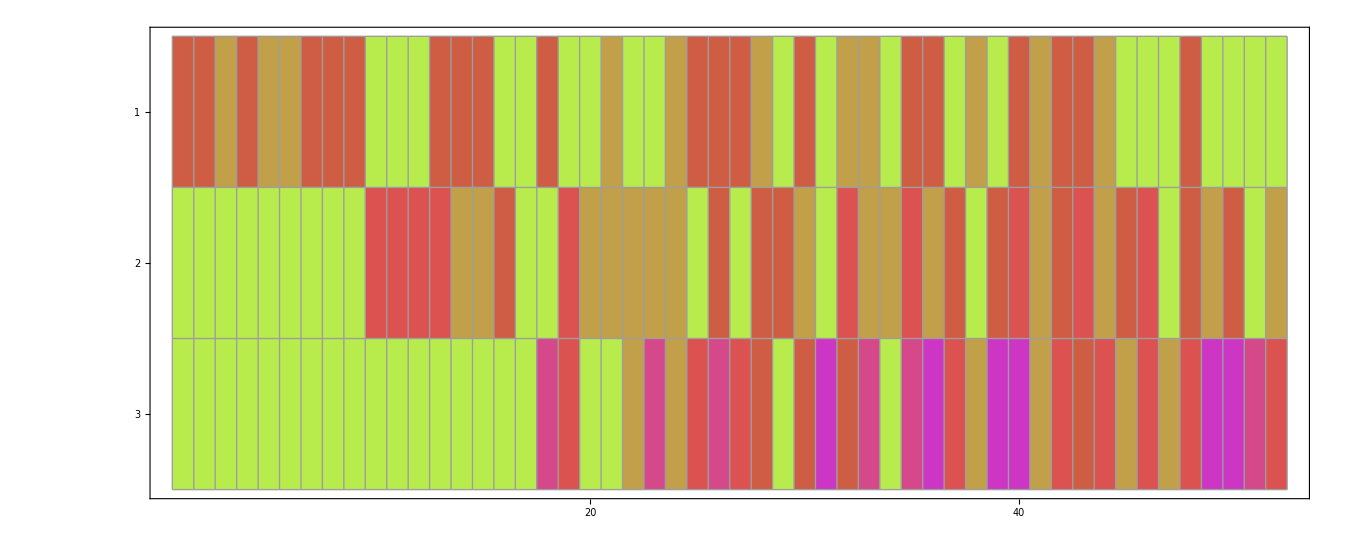

```mathematica
ArrayPlot[Table[ IntegerDigits[1091606241026315893893358160961329375,b,52],{b,{5,7,11}}],Frame->True,FrameTicks->Automatic,Mesh->True,ColorFunction->"NeonColors"]
```

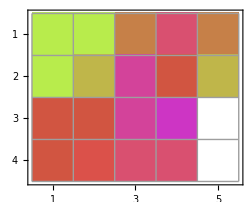

```mathematica
ArrayPlot[Table[ Reverse[IntegerDigits[36179,b]],{b,{11,13,17, 19}}],Frame->True,FrameTicks->Automatic,Mesh->True,ColorFunction->"NeonColors"]
```

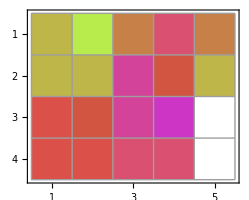

```mathematica
ArrayPlot[Table[ Reverse[IntegerDigits[36180,b]],{b,{11,13,17, 19}}],Frame->True,FrameTicks->Automatic,Mesh->True,ColorFunction->"NeonColors"]
```

```mathematica
Length[ IntegerDigits[306793257528936704771350033337949769541468869706,7]]
```

57

```mathematica
Take[MyList[4,7],{100,100}]
```

{306793257528936704771350033337949769541468869706}

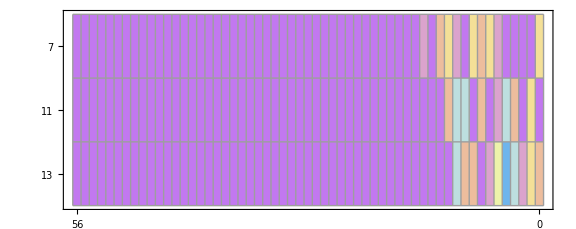
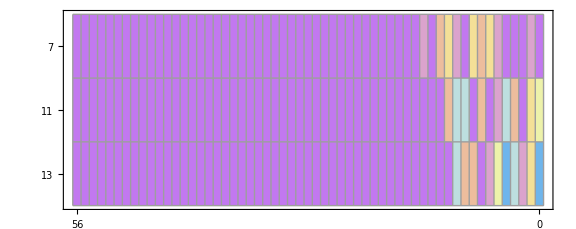
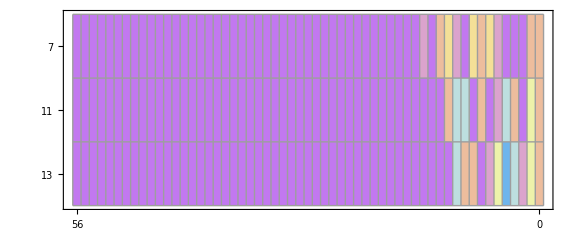
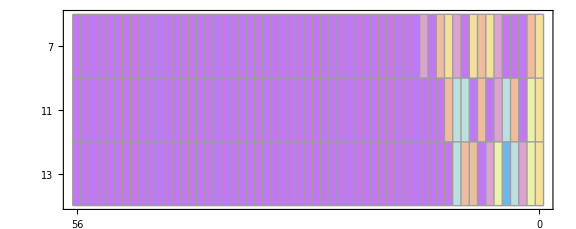
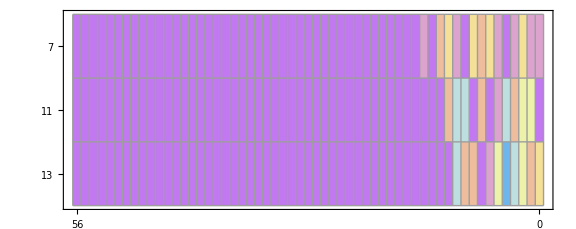
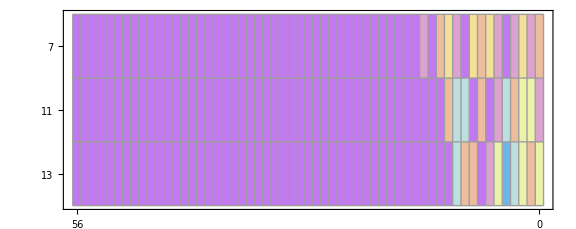
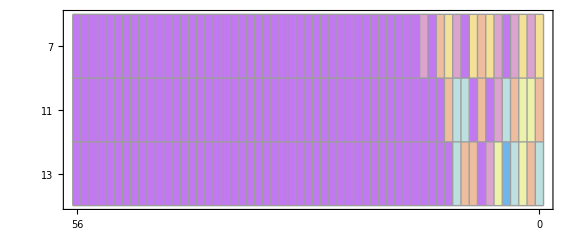
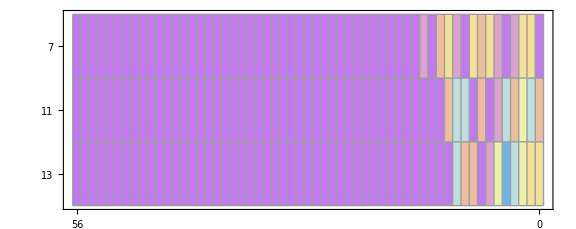

```mathematica
Flatten[Table[ArrayPlot[Table[IntegerDigits[d,b,57],{b,{7,11,13}}], LabelStyle->{ FontFamily->"Calibri"},ColorFunctionScaling->True,Frame->True,  FrameLabel->{{ ,d},{,} },FrameTicks->{{{{1,7},{2,11},{3,13}},All},{{{1,56},{57,0}},None}},Mesh->True,ColorFunction->"Pastel",ImageSize->Large],{d,Take[MyList[4,7],{30,96}]}]]
```

```mathematica
ColorData["Gradients"]
```

```mathematica
{"AlpineColors","Aquamarine","ArmyColors","AtlanticColors","AuroraColors","AvocadoColors","BeachColors","BlueGreenYellow","BrassTones","BrightBands","BrownCyanTones","CandyColors","CherryTones","CMYKColors","CoffeeTones","DarkBands","DarkRainbow","DarkTerrain","DeepSeaColors","FallColors","FruitPunchColors","FuchsiaTones","GrayTones","GrayYellowTones","GreenBrownTerrain","GreenPinkTones","IslandColors","LakeColors","LightTemperatureMap","LightTerrain","MintColors","NeonColors","Pastel","PearlColors","PigeonTones","PlumColors","Rainbow","RedBlueTones","RedGreenSplit","RoseColors","RustTones","SandyTerrain","SiennaTones","SolarColors","SouthwestColors","StarryNightColors","SunsetColors","TemperatureMap","ThermometerColors","ThermometerColors","WatermelonColors"}
```

```mathematica
Select[Table[IntegerString[n,11], {n, MyList[4,11]}],StringMatchQ[#, "*105"] &]
```

{3303352252245105,13414505034403105,50133442552215105,541424101322302305353105,541424101322435255511105,251101122521510352412152105,415324155541413043550152212105,14504040412421214055110544420022230105,14504040412421214055110544520541213105,«13361»,340230014133210151412133435150154351320305215313144555522005405400532454432105,340230014133210151412133435150154351320305215322542053414415043435231425434105,340230014133210151412133435150154351320305215322542053414415043443134314241105,340230014133210151412133435150154351330012541023122112235415014004341455435105,340230014133210151412133435150154351330012541023122112235415014004353330422105,340230014133210151412133435150154351330012541434511241314432440222353235404105,340230014133210151412133435150154351330012541443123524145003020343123524055105,340230014133210151412133435150154351330012541443123524224421053305315300403105}

```mathematica
Table[IntegerString[n,11], {n, MyList[4,11]}]
```

{0,1,2,3,4,5,52,53,301,302,341,5241,5242,5243,5253,5254,5255,5520,5521,5522,5533,5534,5535,21125,25200,25201,25202,25203,25204,25205,25215,25250,25251,43102211242403,43102211242404,43102211242405,43102211242420,43102211242453,43102212524120,43102212524121,43102212543343,43102212543344,43102212543345,43102221214220,43102221214221,43102221214222,43102221214223,43102221214233,43102221214234,43102221214235,43102221214500,43102221214501,43102221214502,43102221214513,43102221214514,43102221432300,43102221433001,43102221433002,43102221433003,43102221433004,1202213140343152,1202213523345031,1202213523345032,1202213523432303,1202213523432304,1202213523451113,1202213523451114,1202213523451115,1202213523451133,1202213523451134,1202213523451135,1202213523451150,1202213523451410,1202213523451411,1202213523451412,1202213523451413,1202213523451414,1202213523451415,1202214242150402,1202214242150403,1202214242150435,1202214242150450,1202214242150451,1202214242150452,1202214243020210,1202214243023521,1202214243023522,1202214243043203,1202214243043204,1202214243043205,1202214243043220,3303352242105540,3303352242142050,3303352252245101,3303352252245102,3303352252245103,3303352252245104,3303352252245105,3303352252245401,3303352252245402}